```mathematica
curr1=Import[NotebookDirectory[]<>"average_gas.csv"];
curr2=Import[NotebookDirectory[]<>"average_gas.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data={curr1[[All,7]],curr2[[All,3]]}//Transpose;
labels=curr1[[All,1]];
ListPlot[data->labels,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●},PlotLabel->"GAS",AxesLabel->{"ELECTRICITY","ETH"},ImageSize->400]
```

-Graphics-

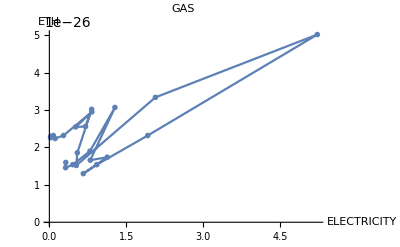

```mathematica
curr1=Import[NotebookDirectory[]<>"average_gas.csv"];
curr2=Import[NotebookDirectory[]<>"average_gas.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data={curr1[[All,7]],curr2[[All,3]]}//Transpose;
labels=curr1[[All,1]];
ListPlot[data,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●},PlotLabel->"GAS",AxesLabel->{"ELECTRICITY","ETH"},ImageSize->400]
Export[NotebookDirectory[]<>"gaselectricityether.pdf",%,"PDF"];
```

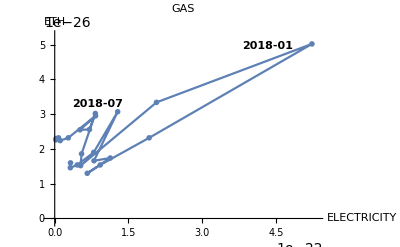
```mathematica
a= -Graphics-
```

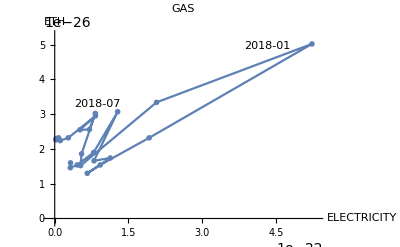

-Graphics-

/Users/Mahsa/Documents/Stable-Coin/stable-coin-paper/code for plots/Gas_Plots/gaselectricityether.pdf

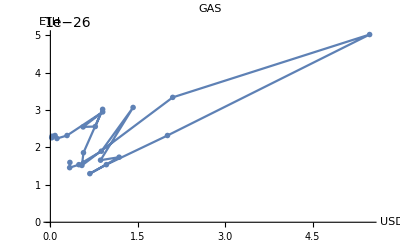

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"gaselectricityether.pdf",a,"PDF"]


curr1=Import[NotebookDirectory[]<>"average_gas.csv"];
curr2=Import[NotebookDirectory[]<>"average_gas.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data={curr1[[All,5]],curr2[[All,3]]}//Transpose;
labels=curr1[[All,1]];
ListPlot[data,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●},PlotLabel->"GAS",AxesLabel->{"USD","ETH"},ImageSize->400]
Export[NotebookDirectory[]<>"gasetherusd.pdf",%,"PDF"];
```

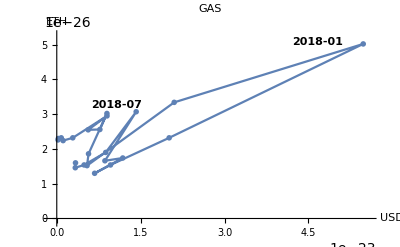
```mathematica
a=-Graphics-
```

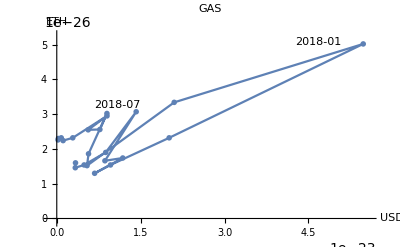

-Graphics-

```mathematica
Show[%147,AxesStyle->Gray]
```

```mathematica
a=-Graphics-
```

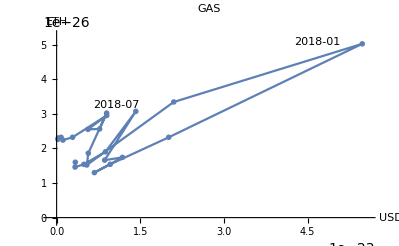

```mathematica
Export[NotebookDirectory[]<>"gasetherusd.pdf",a,"PDF"];
```